

```mathematica
Plot[Sin[x],{x,0,2Pi}]
```

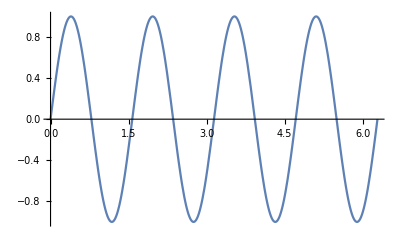

```mathematica
Plot[Sin[4x],{x,0,2Pi}]
```

```mathematica
?Play
```

```mathematica
Play[Sin[256t(2Pi)],{t,0,2}]
```

-Graphics-

```mathematica
Options[Play,SampleRate]
```

{SampleRate→8000}

```mathematica
Play[Sin[8192 2Pi t],{t,0,2}]
```

-Graphics-

```mathematica
RealDigits[N[1/19,20]]
```

{{5,2,6,3,1,5,7,8,9,4,7,3,6,8,4,2,1,0,5,3},-1}

```mathematica
digits=RealDigits[N[1/19,1000]][[1]];
```

```mathematica
ListPlay[digits]
```

-Graphics-

```mathematica
irratdigits=RealDigits[N[Pi,1000]][[1]];
```

```mathematica
ListPlay[irratdigits]
```

-Graphics-

```mathematica
cmajor=Table[N[261.62558 2^(j/12)],{j,0,11}]
```

{261.626,277.183,293.665,311.127,329.628,349.228,369.994,391.995,415.305,440.,466.164,493.883}

```mathematica
notes4=Take[cmajor,4];
```

```mathematica
Do[Play[Sin[notes4[[j]] 2Pi t],{t,0,1}],
{j,1,4}]//Timing
```

{0.171875,Null}

```mathematica
SetAttributes[playTones,Listable]
```

```mathematica
playTones[freq_,time_]:=
Play[Sin[2Pi t freq],{t,0,time}]
```

```mathematica
playTones[notes4,0.5];//Timing
```

{0.015625,Null}

```mathematica
randomnotes=Table[cmajor[[Random[Integer,{1,12}]]],{20}]
```

{415.305,493.883,293.665,493.883,293.665,493.883,329.628,311.127,415.305,466.164,293.665,493.883,415.305,293.665,349.228,415.305,329.628,293.665,261.626,391.995}

```mathematica
playTones[randomnotes,0.5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
step:=Random[Integer,{-2,2}]
```

```mathematica
s20=Table[step,{20}]
```

{-2,1,-1,-2,1,1,2,0,0,-1,-2,0,1,1,-2,2,0,2,2,-2}

```mathematica
FoldList[Plus,6,s20]
```

{6,4,5,4,2,3,4,6,6,6,5,3,3,4,5,3,5,5,7,9,7}

```mathematica
cmajor[[14]]
```

Part::partw: Part 14 of {261.626,277.183,293.665,311.127,329.628,349.228,369.994,391.995,415.305,440.,466.164,493.883} does not exist.

{261.626,277.183,293.665,311.127,329.628,349.228,369.994,391.995,415.305,440.,466.164,493.883}⟦14⟧

```mathematica
pos=Mod[FoldList[Plus,4,s20],11]+1
```

{5,3,4,3,1,2,3,5,5,5,4,2,2,3,4,2,4,4,6,8,6}

```mathematica
brown=cmajor[[pos]]
```

{329.628,293.665,311.127,293.665,261.626,277.183,293.665,329.628,329.628,329.628,311.127,277.183,277.183,293.665,311.127,277.183,311.127,311.127,349.228,391.995,349.228}

```mathematica
brownMusic[n_Integer,r_:2]:=Module[{cmajor,s},
cmajor=Table[N[261.62558 2^(j/12)],{j,0,11}];
s=Table[Random[Integer,{-r,r}],{n}];
cmajor[[Mod[FoldList[Plus,4,s],11]+1]]
]
```

```mathematica
playTones[brownMusic[20],0.5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Play[Sin[1000/x],{x,-2,2}]
```

Power::infy: Infinite expression 1/0. encountered.

-Graphics-

```mathematica
Play[Sin[2^t],{t,10,14}]
```

-Graphics-

```mathematica
squarePlay[freq_,n_,time_]:=
Play[Sum[Sin[freq i 2Pi t]/i,{i,1,n,2}],
{t,0,time}]
```

```mathematica
squarePlay[440,7,.5]
```

-Graphics-

```mathematica
sawPlay[freq_,n_,time_]:=
Play[Sum[Sin[freq i 2Pi t]/i,{i,1,n}],
{t,0,time}]
```

```mathematica
sawPlay[440,6,0.5]
```

-Graphics-

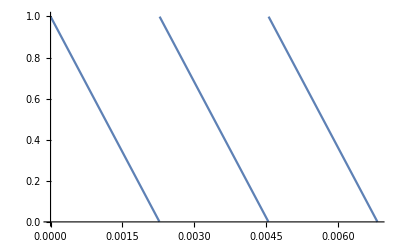

```mathematica
Plot[-440t-Floor[-440t],{t,0,3/440}]
```

```mathematica
Play[-440t-Floor[-440t],{t,0,.5}]
```

-Graphics-

```mathematica
pentatonic[n_Integer,r_:2]:=Module[{pscale,s},
pscale={277.183,311.13,369.99,415.30,466.16,554.37};
s=Table[Random[Integer,{-r,r}],{n}];
pscale[[Mod[FoldList[Plus,3,s],4]+1]]
]
```

```mathematica
playTones[pentatonic[24]]
```

playTones[{415.3,415.3,277.183,415.3,277.183,415.3,311.13,311.13,311.13,311.13,415.3,277.183,369.99,311.13,277.183,369.99,415.3,369.99,369.99,369.99,277.183,369.99,415.3,277.183,277.183}]

```mathematica
tonesAndTimes[n_]:=Module[{cmajor,notes,durs},
cmajor=Table[N[261.62558 2^(j/12)],{j,0,11}];
notes:=Table[cmajor[[Random[Integer,{1,12}]]],{n}];
durs:=Table[1/2^(Random[Integer,{0,3}]),{n}];
MapThread[playTones,{notes,durs}]]
```

```mathematica
d10=Table[Random[Integer,{-2,2}],{10}]
```

{-2,-2,0,-1,0,-1,-2,-1,-1,-1}

```mathematica
Mod[FoldList[Plus,0,d10],4]+1
```

{1,3,1,1,4,4,3,1,4,3,2}

```mathematica
durs={1/8,1/4,1/2,1}[[%]]
```

{1/8,1/2,1/8,1/8,1,1,1/2,1/8,1,1/2,1/4}

```mathematica
s10=Table[Random[Integer,{-2,2}],{10}]
```

{1,2,-1,-1,0,-1,2,2,0,-1}

```mathematica
pos=Mod[FoldList[Plus,0,s10],13]+1
```

{1,2,4,3,2,2,1,3,5,5,4}

```mathematica
tones=cmajor[[pos]]
```

{261.626,277.183,311.127,293.665,277.183,277.183,261.626,293.665,329.628,329.628,311.127}

```mathematica
MapThread[playTones,{tones,durs}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
tonesAndTimes2[n_]:=Module[{cmajor,tones,durs,d,t},
cmajor=Table[N[261.62558 2^(j/12)],{j,0,11}];
d=Table[Random[Integer,{-2,2}],{n}];
durs={1/8,1/4,1/2,1}[[Mod[FoldList[Plus,0,d],4]+1]];
t=Table[Random[Integer,{-2,2}],{n}];
tones=cmajor[[Mod[FoldList[Plus,0,t],13]+1]];
MapThread[playTones,{tones,durs}]]
```

```mathematica
tonesAndTimes2[3]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}